```mathematica
ΔP={6.26,15.6,30.9,106,329,681,1200,1730}
u={1.17,1.95,2.91,5.84,11.13,16.92,23.34,28.73}
ρ=62.3
μ=0.000672
Di=0.04133
l=5

Π1=(ΔP/l)/(Di^-1*ρ*u^2)*32.2
Π2=μ/(ρ*u*Di)
```

{6.26,15.6,30.9,106,329,681,1200,1730}

{1.17,1.95,2.91,5.84,11.13,16.92,23.34,28.73}

62.3

0.000672

0.04133

5

{0.0195374,0.0175274,0.0155896,0.0132783,0.0113467,0.0101627,0.00941115,0.00895443}

{0.000223064,0.000133839,0.0000896856,0.0000446892,0.0000234488,0.0000154247,0.0000111819,9.08406×10^-6}

{{0.000223064,0.0195374},{0.000133839,0.0175274},{0.0000896856,0.0155896},{0.0000446892,0.0132783},{0.0000234488,0.0113467},{0.0000154247,0.0101627},{0.0000111819,0.00941115},{9.08406×10^-6,0.00895443}}

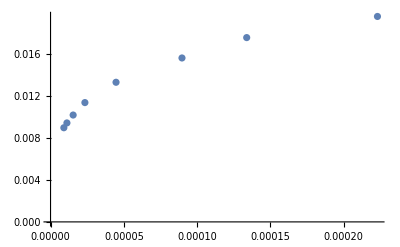

```mathematica
data1= {{0.000223064,0.0195374},{0.000133839,0.0175274},{0.0000896856,0.0155896},{0.0000446892,0.0132783},{0.0000234488,0.0113467},{0.0000154247,0.0101627},{0.0000111819,0.00941115},{9.08406*10^-6,0.00895443}}

ListPlot[data1]
```

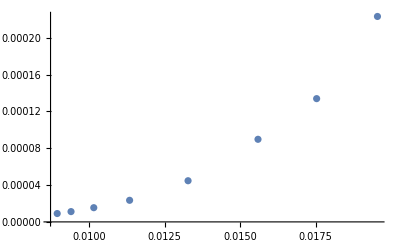

-Graphics-

```mathematica
{{0.000223064,0.0195374},{0.000133839,0.0175274},{0.0000896856,0.0155896},{0.0000446892,0.0132783},{0.0000234488,0.0113467},{0.0000154247,0.0101627},{0.0000111819,0.00941115},{9.084059999999999*^-6,0.00895443}}
```

```mathematica
Fit[data1,{1,Log[x]},x]
```

0.0466432+0.00328375 Log[x]

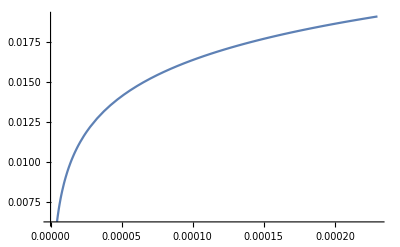

```mathematica
Plot[0.0466431920820853+0.003283751086645133 Log[x],{x,0,0.00023}]
```

```mathematica
lf=NonlinearModelFit[data1, b+a*Log[x],{a,b},x]
lf["RSquared"]
```

FittedModel[0.0466432+0.00328375 Log[x]]

0.999313

```mathematica
Solve[ Exp[0.95*x2^2]*79.80== Exp[0.95*(1-x2)^2]*40.50]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x2→0.143041}}